# Energy barriers

This notebook is used to extract the energy barriers fro the processed thermal collapse data. Data used in this notebook is stored in ParentDirectory[]<>”/data/processed-collapse-times/”.

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
SetOptions[{MatrixPlot,ListVectorPlot},ImageSize->800,ImagePadding->{{50,70},{50,50}},LabelStyle->{Directive["Times",14,Black],FontFamily->"Times"}];
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot,Plot,LogPlot,LogLogPlot,Histogram},Frame->True,AspectRatio->1/GoldenRatio,ImageSize->1000,LabelStyle->{Directive["Times",18,Black],FontFamily->"Times",ImagePadding->{{100,100},{100,100}}}];

DMI = 0.02;
```

Functions

```mathematica
(*

Determines Γ from the list of collapse times ;

Input: nested list of collapse times at various temperatures. {T1, {t1,t2,..},T2,{t1,t2,..},...} ;
Output: proccessed list of temperaure and collapse rate {1/T, Γ};

For explanation of extraction of escape rate from collapse times see: 
D.A.Garanin, Uniform and nonuniform thermal switching of magnetic particles. Phys. Rev. B 98,144425-(12) (2018)
*)
processCollapseTimes[collapseTimes_]:=Block[{gammaValues,cj,jmax,gamRunsList,nRuns,gamm,collapseList,T,j},

gammaValues = {};    
jmax = Length[collapseTimes];

For[j=1, j≤ jmax, j++ ,

T = collapseTimes[[j,1]]; (* get current temperature *)

collapseList = collapseTimes[[j,2]]; 
nRuns = Length[collapseList];
collapseList = Sort[DeleteCases[collapseList,0]];

gamRunsList = Table[-Log[1-(i-0.5)/nRuns]/collapseList[[i]],{i,1,Length[collapseList]}];

gamm = Mean[Drop[gamRunsList,Round[0.1nRuns]]];

AppendTo[gammaValues,{1./T,gamm}];

];
gammaValues
]
```

```mathematica
(*

Input: nested list of collapse times at various temperatures. {T1, {t1,t2,..},T2,{t1,t2,..},...} ;
Output: roccessed list of temperaure and collapse rate {1/T, Γ}
*)
getGammaZeroAndBarrier[collapseTimes_]:=Block[{gammaTinvList,gammaTinvLogList,linearFit,},

gammaTinvList = processCollapseTimes[collapseTimes];
gammaTinvList = DeleteCases[gammaTinvList,Null];
gammaTinvLogList = Thread[{gammaTinvList[[All,1]],Log@(gammaTinvList[[All,2]])}];

linearFit = Fit[gammaTinvLogList,{1,x},x];

{Exp[linearFit[[1]]],-linearFit[[2]][[1]]}
]
```

```mathematica
(*********************** The following functions are for analytical work ***********************)
(* They use equations for a BP skyrmion *)
```

```mathematica
(* Need high precision for the  *)
prec=40;
```

```mathematica
(* Energy of a Belavin-Polyakov skyrmion ;

Input: H = external field, J = Exchange, A = DMI, λ = skyrmion radius ;
Output: float giving the total energy*)
energy[H_,J_,A_,λ_]:=SetPrecision[(4π J-(2 π J aa^2)/(3 λ^2)-4 π H S λ^2/aa^2 Log[1.5+0.681/(λ√Abs[H]/J)]-(4π A S^2)/aa λ Sin[γ])/.{S->1,aa->1,γ->π/2},prec]
```

```mathematica
(*

Gives the order-th derivative of the energy as a function of λ ;

Input: H = external field (must be a number), J = Exchange, A = DMI, λ = skyrmion radius, Output: Int signifying the order of the derivative ;
Output: Float
*)
denergy[H_?NumericQ,J_,A_,λ_,order_]:=SetPrecision[D[energy[H,J,A,l],{l,order}]/.l->λ,prec]
```

```mathematica
(*
Finds the minimum of the first derivative of the energy function. ;

Input: H = external field (must be a number), J = Exchange, A = DMI, λ = skyrmion radius, Output: Float signifying the value of min E'[λ] ;
*)
minDE[H_?NumericQ,J_,A_,λ_]:= λ/.NMinimize[{denergy[H,J,A,λ,1],1<λ<10},{λ},WorkingPrecision->prec][[2]]
```

```mathematica
(*

Input: J = Exchange, A = DMI,
Output: Float value of H at which the first and second derivative of E[λ] are zero ;
*)
findCritH[J_,A_] :=  -H/.FindRoot[denergy[-H,J,A,minDE[-H,J,A,λ],1],{H,0.001,0.00001,.5}];
```

```mathematica
(*

Input: H = external field (must be a number), J = Exchange, A = DMI ;
Output: Value of energy at the minimum point *)
enMinimum[H_,J_,A_]:=Block[{xmin},
xmin = Max[x/.NSolve[{denergy[H,J,A,x,1]==0,x>1.},x]];
energy[H,J,A,xmin]
]
```

```mathematica
(*

Input: H = external field (must be a number), J = Exchange, A = DMI ;
Output: Value of energy at the maximum point *)
enMaximum[H_,J_,A_]:=Block[{xmin},
xmin = Min[x/.NSolve[{denergy[H,J,A,x,1]==0,x>1.},x]];
energy[H,J,A,xmin]
]
```

```mathematica
(*
Input: H = external field (must be a number), J = Exchange, A = DMI ;
Output: Value of energy barrier, difference between energy minimum and maximum 
*)
enBarrier[H_,J_,A_]:=Block[{min,max},

min = enMinimum[H,J,A];
max =enMaximum[H,J,A];

max-min//Abs
]
minRadius[H_,J_,A_]:=Min[x/.NSolve[{denergy[H,J,A,x,1]==0,x>1.},x]]
```

## Extract energy barriers

### Constants

```mathematica
JJ = 1000; (* 1000 Kelvin *)
SS = 1; (* Dimensionless energy is in E/JS^2 *)
DMI=0.02;

μB = 9.274*^-24; (* J/Tesla *)
hbar = 1.05*^-34; (* kg*m^2/s *)
kB = 1.38*^-23 ;(* J/Kelvin *)

kelvToJ = kB; (* conversion from Kelvin to Joules (kg*m^2/s^2) *)
kelvToEv = 0.0000861732814974; (* convert from kelvin to Ev *)
JtoEv = 6.242*^18; (* joules to electron volts *)

convToSec = JJ*kelvToJ/hbar; (* convert from dimensionless gamma to Hz *)
convToEv = JJ*kelvToEv; (* convert to eV *)
convToTesla = JJ kelvToJ/μB; (* convert dimensionless H/JS to Tesla *)
```

```mathematica
(* calculate critical field in analytical and numerical work *)
HcritN = 0.00259;
HcritA = 0.00134;(*findCritH[1,DMI]*)
```

### Far from critical field

```mathematica
(*************************************************************************)
(* Change the range of external fields to the ones for which data exists. *)
Hmin2 = 0.0014; Hmax2 = 0.0025; dH2 = 0.0001;
hValues2 = Range[-Hmin2,-Hmax2,-dH2];
(*************************************************************************)

(* The directory where data is stored *)
relDirProcessed="data/processed-collapse-times-skyrmion/";

(* Initialize storage *)
gammaZero2 = barriers2 = ConstantArray[0,Length[hValues2]];

(* Get processed collapse data as a list of Arrhenius prefactor and energy barriers *)
({gammaZero2[[#]],barriers2[[#]]} =getGammaZeroAndBarrier[ToExpression@Import[relDirProcessed<>"collapse-times_H="<>ToString[hValues2[[#]]]<>".csv","CSV"]
])&/@Range[Length[hValues2]];

Grid[Prepend[Thread[{-hValues2 (*convToTesla*),gammaZero2*convToSec , barriers2(**JJ*kelvToEv*)}],{"H [T]","Γ_0 [Hz]","U_Thermal"}] ,Frame->All]
```

H [T] | Γ_0 [Hz] | U_Thermal
0.0014 | 1.26725×10^11 | 0.564988
0.0015 | 1.32154×10^11 | 0.487927
0.0016 | 1.62236×10^11 | 0.441254
0.0017 | 1.2138×10^11 | 0.368197
0.0018 | 5.11664×10^10 | 0.247043
0.0019 | 8.63979×10^10 | 0.235244
0.002 | 2.87871×10^10 | 0.127241
0.0021 | 3.4175×10^10 | 0.106938
0.0022 | 2.94272×10^10 | 0.0714624
0.0023 | 2.43649×10^10 | 0.0378639
0.0024 | 9.31924×10^9 | 0.0174486
0.0025 | 2.57939×10^10 | 0.0123782

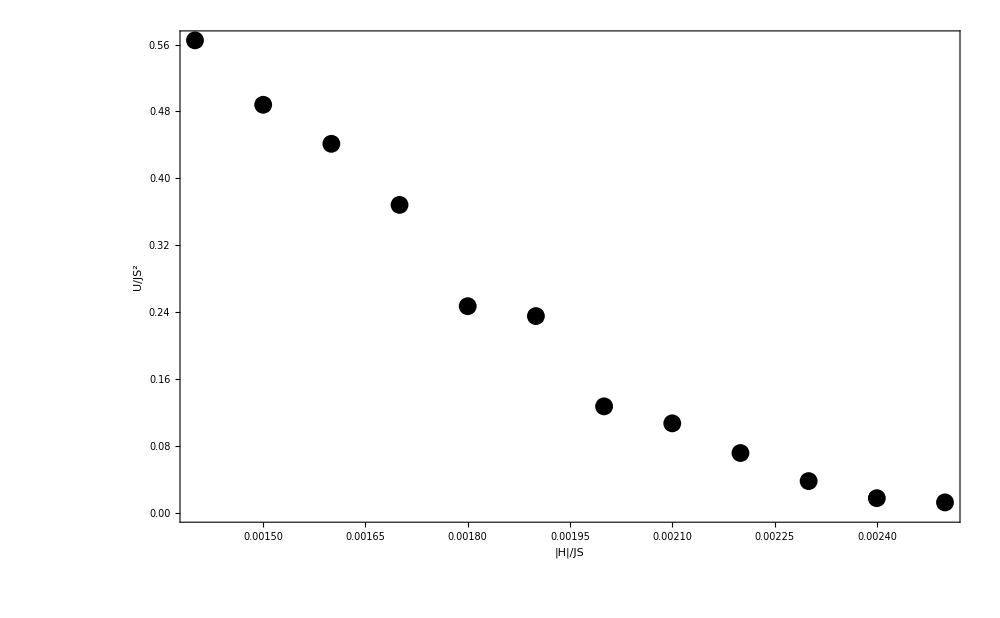

```mathematica
(* Plot the energy barriers as a function of external field. *)
barrierVsFieldPlot = ListPlot[Thread[{-hValues2,barriers2}],FrameLabel->{"|H|/JS","U/JS^2"},PlotRange->All,PlotStyle->Black]
```

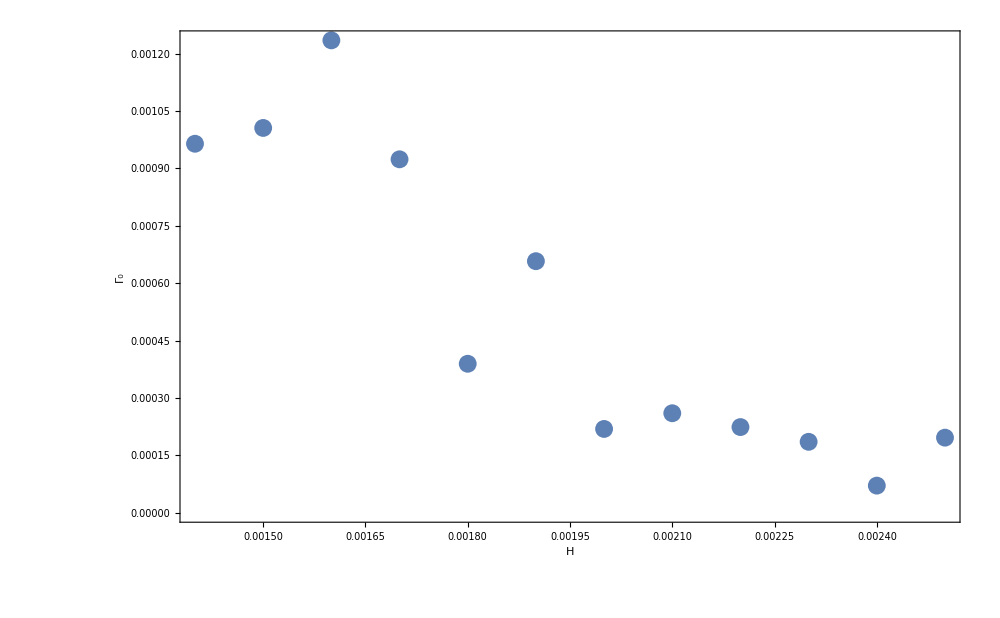

```mathematica
(* Plot the Arrhenius prefactor as a function of external field *)
gammaZeroPlot=ListPlot[Thread[{-hValues2,gammaZero2}],FrameLabel->{"H","Γ_0"},PlotRange->All]
```

### Close to critical field

```mathematica
(*************************************************************************)
(* Change the range of external fields to the ones for which data exists. *)
Hmin = 0.00255; Hmax = 0.002575; dH = 0.000005;
hValues = Range[-Hmin,-Hmax,-dH];
hValues = ReverseSort[Flatten[AppendTo[hValues,{-0.002551,-0.002553,-0.002556,-0.002558,-0.002561,-0.002563,-0.002566,-0.002568}]]];
hValues=DeleteCases[hValues,-0.00256];
hValues=DeleteCases[hValues,-0.002555];
(*************************************************************************)

(* The directory where data is stored *)
relDirProcessed="data/processed-collapse-times-skyrmion/";

epsilonValues = (1-#/HcritN)&/@Abs[hValues];
```

```mathematica
(* Initialize storage *)
gammaZero = barriers = ConstantArray[0,Length[hValues]];

(* Get processed collapse data as a list of Arrhenius prefactor and energy barriers *)
({gammaZero[[#]],barriers[[#]]} =getGammaZeroAndBarrier[ToExpression@Import[relDirProcessed<>"collapse-times_H="<>ToString[hValues[[#]]]<>".csv","CSV"]
])&/@Range[Length[hValues]];

(* Energy barriers from analytical model. Determine those as a function of difference from the analytical model's cricial field. *)
barriersA = enBarrier[-HcritA(1-#),1.,DMI]&/@epsilonValues;

Grid[Prepend[Thread[{hValues (*convToTesla*),epsilonValues,gammaZero*convToSec, barriers*JJ*kelvToEv,barriersA*JJ*kelvToEv}],{"H [T]","ϵ","Γ_0 [Hz]","U_Thermal [eV]","U_Continuous [eV]"}] ,Frame->All]
```

H [T] | ϵ | Γ_0 [Hz] | U_Thermal [eV] | U_Continuous [eV]
-0.00255 | 0.015444 | 8.8495×10^9 | 0.000183896 | 0.000145882
-0.002551 | 0.0150579 | 8.07048×10^9 | 0.000166461 | 0.000140019
-0.002553 | 0.0142857 | 1.1072×10^10 | 0.00018311 | 0.000128547
-0.002556 | 0.0131274 | 8.29863×10^9 | 0.000133564 | 0.000111988
-0.002558 | 0.0123552 | 1.16864×10^10 | 0.000157973 | 0.000101394
-0.002561 | 0.0111969 | 1.07697×10^10 | 0.000135164 | 0.0000861993
-0.002563 | 0.0104247 | 1.10626×10^10 | 0.000126029 | 0.00007655
-0.002565 | 0.00965251 | 9.92477×10^9 | 0.000101229 | 0.0000673011
-0.002566 | 0.00926641 | 1.06392×10^10 | 0.000101993 | 0.0000628316
-0.002568 | 0.00849421 | 1.52477×10^10 | 0.000117214 | 0.0000542133
-0.00257 | 0.00772201 | 1.28178×10^10 | 0.0000922187 | 0.000046039
-0.002575 | 0.00579151 | 1.10743×10^10 | 0.0000542175 | 0.0000277067

```mathematica
(* To find the relationship U = Subscript[H, crit](1-ϵ)^n, take the natural log of the equation and find the linear fit. This  *)
logdata = Thread[{Log[1-(-hValues/HcritN)],Log[barriers]}];
model = aa+nn ϵ;
{a,n} = {aa,nn}/.FindFit[logdata,model,{aa,nn},ϵ]
```

{-1.49371,1.11338}

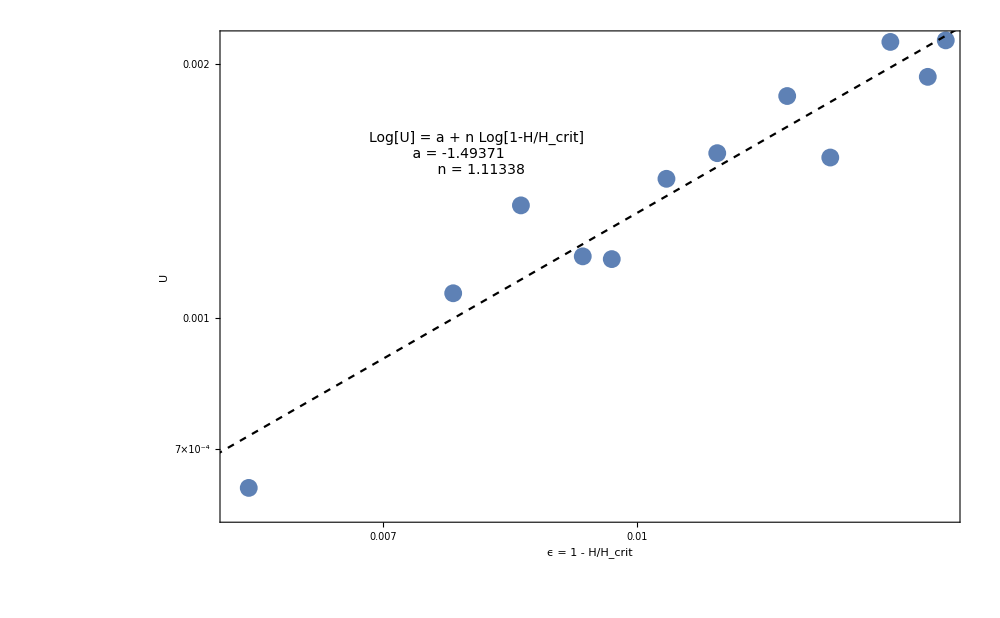

```mathematica
closePlot = Show[ListLogLogPlot[Thread[{1-(-hValues/HcritN),barriers}],FrameLabel->{"ϵ = 1 - H/H_crit","U"},Epilog->{Text[Style["Log[U] = a + n Log[1-H/H_crit] \n a = "<>ToString[a]<>"          \n n = "<>ToString[n]<>"               ",14,FontFamily->"Times"],Scaled[{0.35,0.75}]]}],Plot[model/.{aa->a,nn->n},{ϵ,-100,100},PlotStyle->{Black,Dashed}]]
```

```mathematica
logdata = Thread[{Log[1-(-hValues/HcritN)],Log[barriers]}];
model1 = aa+1.5 ϵ;
{a1} = {aa}/.FindFit[logdata,model1,{aa},ϵ]
```

{0.262267}

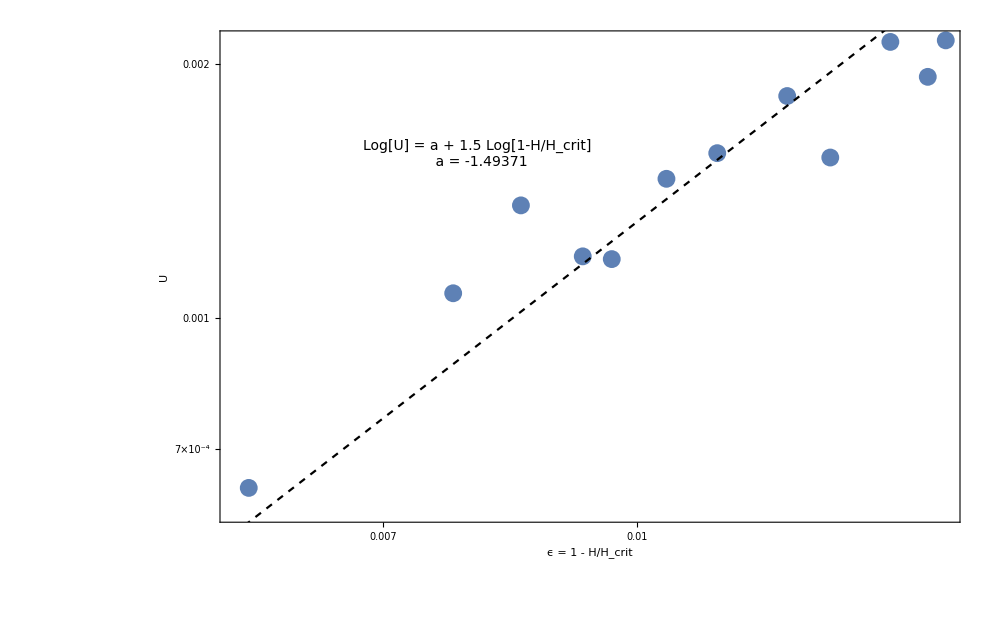

```mathematica
closePlot = Show[ListLogLogPlot[Thread[{1-(-hValues/HcritN),barriers}],FrameLabel->{"ϵ = 1 - H/H_crit","U"},Epilog->{Text[Style["Log[U] = a + 1.5 Log[1-H/H_crit] \n a = "<>ToString[a]<>"           ",14,FontFamily->"Times"],Scaled[{0.35,0.75}]]}],Plot[model1/.{aa->a1},{ϵ,-100,100},PlotStyle->{Black,Dashed}]]
```

### Compare analytical to numerical energy barriers

```mathematica
(*************************************************************************)
(* Change the range of external fields to the ones for which data exists. *)
Hmin2 = 0.0014; Hmax2 = 0.0025; dH2 = 0.0001;
hValues2 = Range[-Hmin2,-Hmax2,-dH2];
hValues2 = ReverseSort[Flatten[AppendTo[hValues2,{-0.0025}]]];
(*************************************************************************)

(* The directory where data is stored *)
relDirProcessed="data/processed-collapse-times-skyrmion/";

(* Initialize storage *)
gammaZero2 = barriers2 = ConstantArray[0,Length[hValues2]];

(* Get processed collapse data as a list of Arrhenius prefactor and energy barriers *)
({gammaZero2[[#]],barriers2[[#]]} =getGammaZeroAndBarrier[ToExpression@Import[relDirProcessed<>"collapse-times_H="<>ToString[hValues2[[#]]]<>".csv","CSV"]
])&/@Range[Length[hValues2]];

epsilonValues2 = (1-#/HcritN)&/@Abs[hValues2];
```

```mathematica
eps = epsilonValues2;(*Range[0.5,0.2,-0.05];*)
hValsA =HcritA(1-#)&/@eps;
barA = enBarrier[-#,1.,DMI]&/@hValsA;
```

```mathematica
Grid[Prepend[Thread[{eps,barA,barriers2}],{"ϵ","U_Analytical","U_Discrete"}],Frame->All]
```

ϵ | U_Analytical | U_Discrete
0.459459 | 0.60903262085508558243418519850820302963 | 0.564988
0.420849 | 0.4915859098404524729630793444812297821 | 0.487927
0.382239 | 0.39397382893097265821324981516227126122 | 0.441254
0.343629 | 0.31244089613909231673005706397816538811 | 0.368197
0.305019 | 0.24414488646684873174308449961245059967 | 0.247043
0.266409 | 0.1869106372851678798951979842968285084 | 0.235244
0.227799 | 0.1390628897207619729670113883912563324 | 0.127241
0.189189 | 0.09931307935669053676974726840853691101 | 0.106938
0.150579 | 0.06668633530420642330227565253153443336 | 0.0714624
0.111969 | 0.04048505547009817462367209373041987419 | 0.0378639
0.0733591 | 0.0203031771999331311917558196000754833 | 0.0174486
0.034749 | 0.00617549278137730084381473716348409653 | 0.0123782
0.034749 | 0.00617549278137730084381473716348409653 | 0.0123782

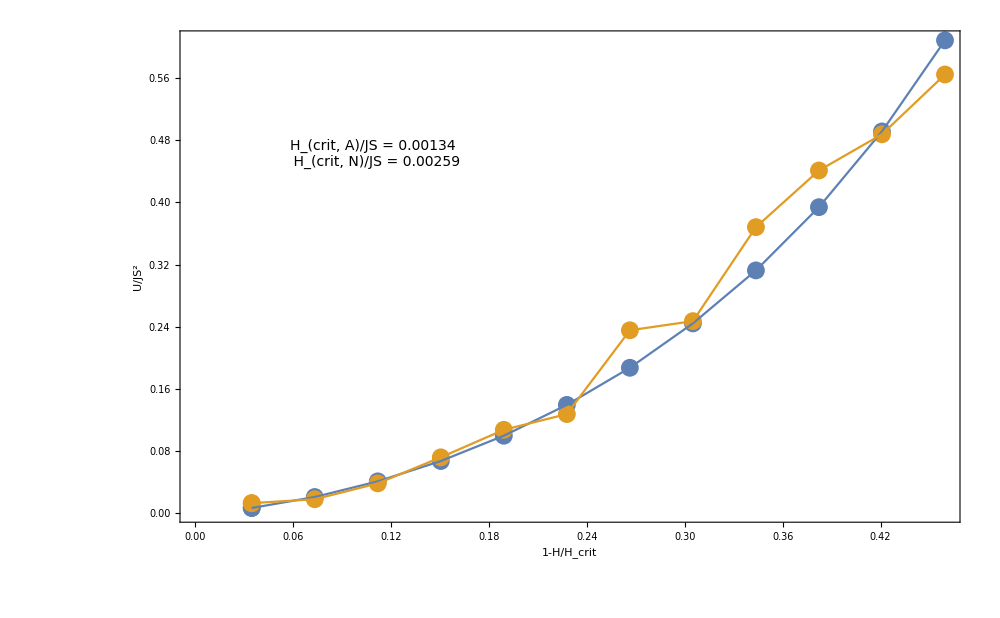

```mathematica
p = Show[ListPlot[{Thread[{eps,barA}],Thread[{eps,barriers2}]},FrameLabel->{"1-H/H_crit","U/JS^2"},Epilog->{Text[Style["H_(crit, A)/JS = 0.00134 \n H_(crit, N)/JS = 0.00259  ",14,FontFamily->"Times"],Scaled[{0.25,0.75}]]}],ListPlot[{Thread[{eps,barA}],Thread[{eps,barriers2}]},Joined->True]]
```

```mathematica
(*Export["plots/barriers-compare.eps",Show[p,ImageSize->18/2.54*72]]*)
```

## Energy Barrier for various damping parameter in LLG

```mathematica
(* Out of curiousity, I wanted to see if changing the damping parameter in the LLG would heavily impact the energy barriers determined. This rough computation does not show any obvious relationshop between damping and the energy barrier. *)
H=-0.0019;dampingValues = Range[0.02,0.1,0.02];
```

```mathematica
(* The directory where data is stored *)
relDirProcessed="data/processed-collapse-times-skyrmion/";

gammaZero = barriers = ConstantArray[0,Length[dampingValues]];
({gammaZero[[#]],barriers[[#]]} =getGammaZeroAndBarrier[ToExpression@Import[relDirProcessed<>"collapse-times-H="<>ToString[H]<>"-damping="<>ToString[dampingValues[[#]]]<>".csv"]])&/@Range[Length[dampingValues]];
```

```mathematica
(* Barrier didn't change much for different damping values, but would be useful to have more data *)
showData = Thread[{dampingValues,gammaZero convToSec,barriers convToEv }];
Grid[Prepend[showData,{"λ","Γ_0","U"}],Frame->All]
```

λ | Γ_0 | U
0.02 | 9.8778×10^10 | 0.0186301
0.04 | 1.47974×10^11 | 0.0192723
0.06 | 1.51079×10^11 | 0.0182249
0.08 | 1.10508×10^11 | 0.015282
0.1 | 2.01586×10^11 | 0.0183358